# The Rabi problem

## Yen Lee Loh, 2023-6-24

## Section Spin in constant magnetic field

### Section.Subsection Classical analysis

According to classical magnetostatics, a magnetic moment m̲ in a magnetic field B̲ experiences a torque τ̲=m̲×B̲.
According to classical mechanics, angular momentum is related to torque by d/dt J̲=τ̲.
For many types of objects, magnetic moment and angular momentum are related as m̲=γ J̲ where γ is the gyromagnetic ratio. 
Such an object, when placed in a magnetic field, will precess according to
	d/dt J̲=γ J̲×B̲
∴	d/dt J̲=-γ B̲×J̲
∴	d/dt J̲=ω̲×J̲
where ω̲=-γ B̲ is the Larmor angular frequency vector.  The angular momentum precesses in the sense defined by the direction of ω̲.

### Section.Subsection Quantum mechanical analysis

A spin in a constant magnetic field is described by the Hamiltonian
	Ĥ=-(g μ_B)/ℏB̲·UnderBar[Ŝ]=ω̲·UnderBar[Ŝ]
where ω̲=-(g μ_B)/ℏ B̲ is the Larmor angular frequency vector.  The unitary time-evolution operator is
	Û=e^(-i Ĥ t/ℏ)=e^(-iω̲·UnderBar[Ŝ]/ℏ)=e^(-iθ̲·UnderBar[Ŝ]/ℏ)
where θ̲=ω̲ t is the axis-angle vector corresponding to the full spin rotation.

For a spin-half spin, we may write the unitary time-evolution operator.08in the standard representation as
	UnderBar[U̲]=(cos θ/2-(i θ_z)/θ sin θ/2 | (-θ_y-i θ_x)/θ sin θ/2
(θ_y-i θ_x)/θ sin θ/2 | cos θ/2+(i θ_z)/θ sin θ/2).

From Ehrenfest’s theorem,
	d/dt⟨UnderBar[Ŝ]⟩=1/iℏ⟨[Ŝ,Ĥ]⟩
		 =-i/ℏ⟨[Ŝ,ω̲·UnderBar[Ŝ]]⟩
∴	d/dt⟨(Ŝ)_i⟩=-i/ℏ⟨[(Ŝ)_i,ω_j(Ŝ)_j]⟩
		   =-i/ℏ ω_j⟨[(Ŝ)_i,(Ŝ)_j]⟩
		   =-i/ℏ ω_j⟨i ℏε_ijk(Ŝ)_k⟩
		   =ε_ijk ω_j⟨(Ŝ)_k⟩
∴	d/dt⟨UnderBar[Ŝ]⟩=ω̲×⟨UnderBar[Ŝ]⟩
which is identical to the classical result.

## Section Spin in oscillating magnetic field

Now consider a spin in a steady field B_z and an oscillating field B_x cos νt.  Suppose the Hamiltonian, in some units, is
	UnderBar[H̲]=(b_z | b_x cos νt
b_x cos νt | -b_z).
The equation of motion is
	d/dt ψ_↑=-i b_z ψ_↑-i(b_x cos νt)ψ_↓
	d/dt ψ_↓=+i b_z ψ_↓-i(b_x cos νt)ψ_↑
It is not possible to solve these in terms of named special functions.  But we may proceed as follows.  Go to the interaction picture:

ψ_↑=e^(-i b_z t)c_↑
	ψ_↓=e^(+i b_z t)c_↓.
Then the ODEs become
	d/dt c_↑=-i(b_x cos νt)e^(+2i b_z t)c_↓=-i/2b_x(e^iνt+e^-iνt)e^(+2i b_z t)c_↓
	d/dt c_↓=-i(b_x cos νt)e^(-2i b_z t)c_↑=-i/2b_x(e^iνt+e^-iνt)e^(-2i b_z t)c_↑.
Now make the rotating-wave approximation.  Discard quickly-varying terms and keep only slowly-varying terms, assuming that ν≈2 b_z=Ω.  Then
	d/dt c_↑≈-i/2 b_x e^(i(Ω-ν)t)c_↓
	d/dt c_↓≈-i/2 b_x e^(i(ν-Ω)t)c_↑.
So
	d/dt c_↑≈-i/2 b_x e^-iδt c_↓
	d/dt c_↓≈-i/2 b_x e^(+iδt)c_↑
where δ=Ω-ν is the detuning.  Make yet another transformation: c_↑=e^(-iδt/2)C_↑ and c_↓=e^(+iδt/2)C_↓.  Then
	e^(-iδt/2)(d/dt C_↑-iδ/2 C_↑)≈-i/2 b_x e^-iδt e^(+iδt/2)C_↓	∴	d/dt C_↑-iδ/2 C_↑=-i/2V C_↓		where V≡b_x is perturbation strength
	e^(+iδt/2)(d/dt C_↓+iδ/2 C_↓)≈-i/2 b_x e^(+iδt)e^(-iδt/2)C_↑	∴	d/dt C_↓+iδ/2 C_↓=-i/2V C_↑.

This is a set of coupled 1st order ODEs.

Zero detuning
If the detuning is δ=0 then we simply have ḟ=-i V/2 g and ġ=-i V/2 f.  So f^(..)=-V^2/4 f.   So both things just vary in quadrature

General

One way to solve this is to combine into a single 2nd order ODE.  Eliminate C_↑ by writing C_↑=(d/dt C_↓+iδ/2 C_↓)/(-iV/2).  Then
	d/dt(d/dt C_↓+iδ/2 C_↓)/(-iV/2)-iδ/2(d/dt C_↓+iδ/2 C_↓)/(-iV/2)=-i/2V C_↓
∴	(2i)/V((C^(..))_↓+iδ/2(Ċ)_↓)+δ/V((Ċ)_↓+iδ/2 C_↓)=-i/2V C_↓
∴	(C^(..))_↓+iδ/2(Ċ)_↓+δ/(2i)((Ċ)_↓)+δ/(2i)iδ/2 C_↓=-V^2/4 C_↓
∴	(C^(..))_↓+δ^2/4 C_↓=-V^2/4 C_↓
∴	(C^(..))_↓=-((δ^2+V^2)/4)C_↓

Another way is guess a solution whose time dependence is e^-iΩt:
	C_↑(t)=A e^-iΩt
	C_↓(t)=B e^-iΩt.
Then we obtain
	(Ω+δ/2)A=V/2 B
	(Ω-δ/2)B=V/2 A
∴	B/A=(Ω+δ/2)/(V/2)=(V/2)/(Ω-δ/2)
∴	Ω^2-(δ/2)^2=(V/2)^2
∴	Ω=√((δ/2)^2+(V/2)^2)
∴	(C_↑(t)
C_↓(t))=(V/2/(Ω+δ/2)
1)B e^-iΩt.

Another solution is
∴	(C_↑(t)
C_↓(t))=(V/2/(-Ω+δ/2)
1)B e^(+iΩt).

Suppose at time t=0, C_↑=1 and C_↓=0.  Then the solution must be of the form 
	(C_↑(t)
C_↓(t))=(V/2/(Ω+δ/2)
1)B e^-iΩt-(V/2/(-Ω+δ/2)
1)B e^(+iΩt).
and also
	((V/2)/(Ω+δ/2)+(V/2)/(Ω-δ/2))B=1
∴	V/2(2Ω)/(Ω^2-(δ/2)^2)B=1
∴	V/2(2Ω)/(V/2)^2 B=1
∴	(2Ω)/(V/2)B=1
∴	B=V/(4Ω)=V/(2 √(V^2+δ^2))
∴	C_↓(t)=V/(2 √(V^2+δ^2))(-2i sin Ωt)
∴	P_↓(t)=V^2/(V^2+δ^2)sin^2 Ωt		where Ω=√((δ/2)^2+(V/2)^2) where δ=Ω-ν.
The max transition probability is 1-δ^2/(V^2+δ^2) (depends on detuning) and the Rabi frequency Ω is mainly due to V (perturbation strength) but also depends weakly on detuning.

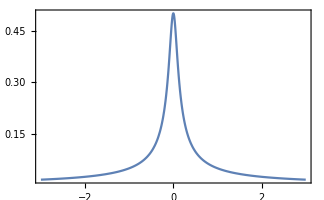

```mathematica
Plot[V/(2 √(δ^2+V^2))/.V->.1,{δ,-3,3},PlotRange->All]
```

Most generally we can think about the case where
	B̲(t)=(B̲)_steady+(B̲)_oscil cos ωt
but the result should be pretty much the same as what we got here.

## Section Two spins with Heisenberg interaction

### Section.Subsection Ehrenfest analysis

Suppose two spins interact via the quantum Hamiltonian
	Ĥ=-JUnderBar[Ŝ]_1·UnderBar[Ŝ]_2.

From Ehrenfest’s theorem,
	d/dt⟨UnderBar[Ŝ]_2⟩=1/iℏ⟨[(Ŝ)_2,Ĥ]⟩
		 =-i/ℏ⟨[(Ŝ)_2,-JUnderBar[Ŝ]_1·UnderBar[Ŝ]_2]⟩
∴	d/dt⟨(Ŝ)_(2i)⟩=-i/ℏ⟨[(Ŝ)_(2i),-J(Ŝ)_(1j)(Ŝ)_(2j)]⟩
		   =i/ℏ J⟨(Ŝ)_(1j)[(Ŝ)_(2i),(Ŝ)_(2j)]⟩
		   =i/ℏ J⟨(Ŝ)_(1j)i ℏε_ijk(Ŝ)_(2k)⟩
		   =-J ε_ijk⟨(Ŝ)_(1j)(Ŝ)_(2k)⟩+
∴	d/dt⟨UnderBar[Ŝ]_2⟩=-J⟨UnderBar[Ŝ]_1×UnderBar[Ŝ]_2⟩.
By symmetry,
	d/dt⟨UnderBar[Ŝ]_1⟩=-J⟨UnderBar[Ŝ]_2×UnderBar[Ŝ]_1⟩.

If the initial state was a non-entangled (direct product) state |Ψ⟩=|(s̲)_1⟩⊗|(s̲)_2⟩, then initially, ⟨UnderBar[Ŝ]_1×UnderBar[Ŝ]_2⟩=⟨UnderBar[Ŝ]_1⟩×⟨UnderBar[Ŝ]_2⟩=(s̲)_1×(s̲)_2.  If we assume that the state remains non-entangled for all time, then we have a pair of simultaneous ODEs,
	d/dt⟨UnderBar[Ŝ]_1⟩=-J⟨UnderBar[Ŝ]_2⟩×⟨UnderBar[Ŝ]_1⟩	
	d/dt⟨UnderBar[Ŝ]_2⟩=-J⟨UnderBar[Ŝ]_1⟩×⟨UnderBar[Ŝ]_2⟩,
which can be solved to show that both spins precess around their average.  This is almost the same as the classical result.  Classically, as far as the second spin is concerned, Ĥ=(ω̲)_2·UnderBar[Ŝ]_2 where (ω̲)_2=-J UnderBar[Ŝ]_1 is the effective field due to the first spin acting on the second spin, i.e., the instananeous Larmor angular frequency vector of the second spin.  Classically, we expect that the second spin will experience a torque (τ̲)_2=(m̲)_2×(B̲)_2=-(S̲)_2×(ω̲)_2.  (I am being cavalier with units.)  Spin angular momentum is related to torque by d/dt(S̲)_2=(τ̲)_2.  So d/dt(S̲)_2=(ω̲)_2×(S̲)_2 and d/dt(S̲)_1=(ω̲)_1×(S̲)_1.  This leads to a typical picture of a classical spin wave as shown in condensed matter textbooks.

However, it is NOT true that the state remains non-entangled!  Let us see what happens in the full calculation below.

### Section.Subsection Quantum mechanical analysis

Now do the full calculation.  If the system evolves under the influence of the Heisenberg interaction J for a time t, the unitary time-evolution operator is
	Û=e^(-i Ĥ t/ℏ)=e^(iJtUnderBar[Ŝ]_1·UnderBar[Ŝ]_2/ℏ)=e^(-iθ/2UnderBar[Ŝ]_1·UnderBar[Ŝ]_2)
where the parameter θ=-2Jt/ℏ is proportional to the interaction strength times the duration.  This is a Heisenberg (SS) interaction gate:
	UnderBar[U̲]=UnderBar[R̲]_SS(θ)=exp(-iθ/2UnderBar[S̲]_1·UnderBar[S̲]_2)=(e^(-iθ/2) | 0 | 0 | 0
0 | e^(iθ/2)cos θ | -i e^(iθ/2)sin θ | 0
0 | -i e^(iθ/2)sin θ | e^(iθ/2)cos θ | 0
0 | 0 | 0 | e^(-iθ/2)).

If one starts with |Ψ⟩=|↑↑⟩=|00⟩, then nothing happens to the state.

But if one starts with |Ψ⟩=|↑↓⟩=|01⟩, then
	Ψ̲(t)=exp(-iθ/2UnderBar[S̲]_1·UnderBar[S̲]_2)Ψ̲(0)=(0
e^(iθ/2)cos θ
-i e^(iθ/2)sin θ
0)∝(cos θ)|01⟩-(i sin θ)|10⟩.
For θ=π/4 we have Ψ̲(t)=1/(√2)|01⟩-i 1/(√2)|10⟩.  This is a maximally entangled state (related to one of the Bell states)!

Using a SS gate it is possible to go from a non-entangled state to an entangled state.

I’m not convinced that RSS allows us to implement CZ or CX though.

## Initialization cells (best version as of 2022-5-5)

### Section.Subsection Basics

```mathematica
Solid=Dashing@{};
DarkGreen=Darker[Green,0.67];
resistorColorList={Black,Brown,Red,Orange,Darker@Yellow,Darker@Green,Blue,Purple,Gray,Cyan};
resistorStyle[n_Integer]:={AbsoluteThickness@1,resistorColorList[[Mod[n,Length@resistorColorList,1]]]};
purpleWhite[v_]:=Hue[0.75,0.25,Abs[v]^0.5];
blueWhiteRed[v_]:=Hue[If[v>0.5,0.0,0.5],(2Abs[v-0.5]),0.95];
colorFromComplex[z_,OptionsPattern[{Brightness->1.}]]:=Hue[Rescale[Arg@z,{0,2 π}],0.8,1-1/(1+Abs[z*OptionValue[Brightness]])];
enlargeFont=#/.s_String->Style[s,16]&;
myCF=Blend[{
Hue[0.8,0.75,0.75],
Hue[0.7,0.75,0.80],
Hue[0.6,0.75,0.90],
Hue[0.6,0.25,1.00],
White,
RGBColor[0.9938925000000001,0.989345,0.5766145],
RGBColor[0.955963,0.863115,0.283425],
RGBColor[0.881316,0.5539655,0.2226795],
RGBColor[0.817319,0.134167,0.164218]},
Clip[#,{0,1}]]&;
myCF=Blend[{
Hue[0.67,0.75,0.80],
White,
Hue[.15,.75,.80]},
Clip[#,{0,1}]]&;
```

```mathematica
myGS={};myPS={LabelStyle->{14,FontFamily->"Times",Black},ImageSize->324,RotateLabel->False,Frame->True,FrameStyle->Directive@{AbsoluteThickness@0,Black},ImageMargins->1};
SetOptions[Graphics,myGS];
SetOptions[Plot,myGS,myPS,ExclusionsStyle->Automatic];
SetOptions[ParametricPlot,myGS,myPS,ExclusionsStyle->Automatic];
SetOptions[ListPlot,myGS,myPS];
SetOptions[ListLinePlot,myGS,myPS];
SetOptions[ListLogPlot,myGS,myPS];
SetOptions[ListLogLogPlot,myGS,myPS];
SetOptions[ListLogLinearPlot,myGS,myPS];
SetOptions[DiscretePlot,myGS,myPS];
SetOptions[RectangleChart,myGS,myPS];
SetOptions[ArrayPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[ContourPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[DensityPlot,myGS,myPS,AspectRatio->Automatic,PlotRangePadding->0];
SetOptions[StreamPlot,myGS,myPS,AspectRatio->Automatic,StreamColorFunction->None,StreamStyle->AbsoluteThickness@1];
SetOptions[Graphics3D,PlotRange->All,ImageSize->600,ViewPoint->{-1,-2,1},ViewVertical->{0,0,1},Lighting->"Neutral",Boxed->False,AspectRatio->Automatic];
```

### Section.Subsection Dimension lines (relatively new code: 2021-2-16)

```mathematica
(*---- USER MAY WANT TO TWEAK ARROWSIZE ----*)
dimLine[r1_,r2_,label_,tickLen_,arrowOffset_,labelOffset_]:=Module[{p,u,v,w,
arrowSize=0.015,
grAH=
Graphics[Line@{{-1,.3},{0,0},{-1,-.3}}]
(*Graphics[Polygon@{{-1,.5},{0,0},{-1,-.5}}]*)
},
p=r2-r1;u=Normalize@{-p⟦2⟧,p⟦1⟧};p=Normalize@p;
(*-------- CHECK IF DIMENSION IS SUFFICIENTLY LARGE --------*)
If[
Norm[r2-r1]>.8    (*5Max[tickLen,arrowOffset,labelOffset]*)
,
(*-------- ORDINARY INTERIOR DIMENSION LINE --------*)
{
Arrowheads[{{-arrowSize,Automatic,grAH},{arrowSize,Automatic,grAH}}],Arrow@{r1+arrowOffset*u,r2+arrowOffset*u},
Line@{{r1,r1+tickLen*u},{r2,r2+tickLen*u}},
Text[label,.55r1+.45r2+labelOffset*u]
},
(*-------- SPECIAL EXTERIOR DIMENSION LINE --------*)
{
exteriorLength=1;
Arrowheads[{{arrowSize,Automatic,grAH}}],
Arrow@{r2+exteriorLength*p+arrowOffset*u,r2+arrowOffset*u},
Arrow@{r1-exteriorLength*p+arrowOffset*u,r1+arrowOffset*u},
Line@{{r1,r1+tickLen*u},{r2,r2+tickLen*u}},
Text[label,.55r1+.45r2+labelOffset*u]
}
]
];
groundSymbol[{x_,y_},s_]:=(
Line@{{{0,3},{0,6}},{{-3,3},{3,3}},{{-2,2},{2,2}},{{-1,1},{1,1}}}
)//Translate[#,{0,-6}]&//Scale[#,s,{0,0}]&//Translate[#,{x,y}]&;
```

### Section.Subsection myFormat

```mathematica
(*-------- Pretty-print any real number --------*)
myFormat[v_]:=(
Which[
(*---- If v is an exact power of 10 with an exponent less than -4 or greater than +4, display v as 10^w ----*)
v>0&&Abs@Log10@v>5&&FractionalPart[Log10@v]==0,SuperscriptBox[10,Round@Log10@v],
(*---- If v is an integer, display v without any decimal points ----*)
Abs[v-Round@v]<10^-8,Round@v,
(*---- If v is not an integer, display v with decimals and possibly in scientific notation ----*)
True,NumberForm[N@v,ExponentFunction->(If[-4<#<4,Null,#]&),NumberPoint->"."]
](*//Style[#,FontWeight->Bold]&*));
```

### Section.Subsection Axis utilities: divisions, etc.

Let v be the numerical part of a physical quantity, and let x be the coordinate along the axis on which this quantity is plotted.
For example, suppose we are displaying 200 GHz at coordinate 8.3.  Then v=200×10^11 and x=8.3.
We will supply a conversion function vfromx to the myAxis function.

```mathematica
(*-------- Plotting parameters --------*)
maxMajorDivisions=30;
maxMinorDivisions=300;
tickLengthMajorP=0.25;
tickLengthMajorM=0.;
tickLengthMinorP=0.15;
tickLengthMinorM=0.;
textOffset=1.5;
(*-------- Round up or down to closest number in a list --------*)
roundUp[x_,xlist_]:=Min@Select[xlist,#≥x&];
roundDn[x_,xlist_]:=Max@Select[xlist,#≤x&];
(*-------- Round up or down to the nearest number of the form 1×10^n, 2×10^n, or 5×10^n --------*)
roundUpNicely[x_]:=Module[{expon},expon=Floor@Log10[x];roundUp[x/10^expon,{1,2,5,10}]*10^expon];
roundDnNicely[x_]:=Module[{expon},expon=Floor@Log10[x];roundDn[x/10^expon,{1,2,5,10}]*10^expon];
(*-------- Divide an interval to find a nice set of tick values --------*)
divisions[{vmin_,vmax_},maxDivisions_]:=Module[{vrange,vstep,vstart,lmin,lmax,v,divs},
vrange=vmax-vmin;
vstep=roundUpNicely[vrange/maxDivisions];
vstart=vstep*Ceiling[vmin/vstep];
divs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
Return@divs;
];
(*-------- Divide an interval to find nice major and minor tick values --------*)
divisions[{vmin_,vmax_},{maxMajorDivisions_,maxMinorDivisions_}]:=Module[{vrange,vstep,vstart,lmin,lmax,v,majDivs,minDivs},
vrange=vmax-vmin;
vstep=roundUpNicely[vrange/maxMajorDivisions]; (* major division spacing *)
vstart=vstep*Ceiling[vmin/vstep];
majDivs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
vstep=roundUpNicely[vstep/maxMinorDivisions]; (* minor division spacing *)
vstart=vstep*Ceiling[vmin/vstep];
minDivs=Select[Range[vstart,vmax,vstep],vmin≤#≤vmax&];
minDivs=Complement[minDivs,majDivs];
Return@{majDivs,minDivs}];
(*-------- Divide an interval with major ticks as 10^n and minor ticks as {2,3,4,5,6,7,8,9}×10^n --------*)
(*-------- This works well except when we have a very small interva --------*)
logDivisions[{vmin_,vmax_}]:=Module[{lmin,lmax,v,majDivs,minDivs}, (* l===Log10[v] *)
lmin=Floor@Log10@vmin;
lmax=Ceiling@Log10@vmax;
majDivs=Table[v=10^l;If[vmin≤v≤vmax,Sow@v],{l,lmin,lmax}]//Reap//Last//Last;
minDivs=Table[v=10^l*mantissa;If[vmin≤v≤vmax,Sow@v],{l,lmin,lmax},{mantissa,2,9}]//Reap//Last//Last;
Return@{majDivs,minDivs}];
linScale[label_,{xmin_,xmax_},vx_]:=Module[{vmin,vmax,xv,x},
xv=InverseFunction[vx];
{vmin,vmax}=Sort@(vx/@{xmin,xmax});
{vlist,vlist2}=divisions[{vmin,vmax},{30,6}];
vlist2=Flatten@vlist2;
Graphics[{
(*-------- Draw axis line and axis label --------*)
Text[label,{xmin,0},{2.00,0}],
{Line@{{xmin,0},{xmax,0}}},
(*-------- Draw major and minor tick marks --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMajorM},{x,tickLengthMajorP}}],{v,vlist}],
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMinorM},{x,tickLengthMinorP}}],{v,vlist2}],
(*-------- Draw major tick labels --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Text[v//myFormat//DisplayForm,{x,0},{0,textOffset}]],{v,vlist}]
},
PlotRange->{{xmin,xmax},{-.5,.5}},PlotRangePadding->{{Scaled@.05,Scaled@.01},{0,0}},
ImageSize->{1200,50},AspectRatio->Full,BaseStyle->{18,FontFamily->"Times"}]
];
logScale[label_,{xmin_,xmax_},vx_]:=Module[{vmin,vmax,xv,x},
xv=Quiet@InverseFunction[vx];
{vmin,vmax}=Sort@(vx/@{xmin,xmax});
{vlist,vlist2}=myLogDivisions[{vmin,vmax}];vlist2=Flatten@vlist2;
(*-------- Draw axis line and axis label --------*)
Graphics[{
Text[label,{xmin,0},{2.00,0}],
Line@{{xmin,0},{xmax,0}},
(*-------- Draw major and minor tick marks --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMajorM},{x,tickLengthMajorP}}],{v,vlist}],
Table[x=xv[v];If[xmin≤x≤xmax,Line@{{x,-tickLengthMinorM},{x,tickLengthMinorP}}],{v,vlist2}],
(*-------- Draw major tick labels --------*)
Table[x=xv[v];If[xmin≤x≤xmax,Text[v//myFormat//DisplayForm,{x,0},{0,textOffset}]],{v,N@vlist}]
},
PlotRange->{{xmin,xmax},{-.5,.5}},PlotRangePadding->{{Scaled@.05,Scaled@.01},{0,0}},
ImageSize->{1200,50},AspectRatio->Full,BaseStyle->{18,FontFamily->"Times"}]
];
mark[x_,label_]:=Module[{},
{Line@{{x,-10},{x,-.5}},
Text[label,{x,-.5}]}
];
 stackScales[grList_]:=Module[{nmax=Length@grList},
Graphics[{
Table[
(*Inset[grList⟦n⟧,{0,-n}]*)
Translate[grList⟦n⟧⟦1⟧,{0,-n}]
,{n,nmax}],
},
ImageSize->{1200,50*nmax},AspectRatio->Full,
PlotRange->{All,{-nmax-.7,-.1}}
]
]
makeLabeledTicks[xmin_,xmax_]:=Module[{xMajorTicks,xMinorTicks,nMajorTicks=10,nMinorTicks=5,func=myFormat},
{xMajorTicks,xMinorTicks}=divisions[{xmin,xmax},{nMajorTicks,nMinorTicks}];
Join[
{N@#,func@#,{.02,0}}&/@xMajorTicks,
{N@#,Null,{.01,0}}&/@xMinorTicks
]
];
makeUnlabeledTicks[xmin_,xmax_]:=Module[{xMajorTicks,xMinorTicks,nMajorTicks=10,nMinorTicks=5,func=Null&},
{xMajorTicks,xMinorTicks}=divisions[{xmin,xmax},{nMajorTicks,nMinorTicks}];
Join[
{N@#,func@#,{.02,0}}&/@xMajorTicks,
{N@#,Null,{.01,0}}&/@xMinorTicks
]
];
```

### Section.Subsection autoTicksLabeled, etc.

```mathematica
decimalExponent[x_]:=Floor@Log10[x];
decimalMantissa[x_]:=x/(10^Floor@Log10[x]);
roundUpNicely[x_]:=SelectFirst[{1,2,5,10},#≥decimalMantissa[x]&]*10^decimalExponent[x];
divisions[{xmin_,xmax_},xstep_]:=Range[Ceiling[xmin,xstep],xmax,xstep]//Select[#,xmin≤#≤xmax&]&;
```

```mathematica
autoTicks$TickColor=White; (* MAY NEED TO SET THIS THING *)
autoTicks$TickColor=Black; (* MAY NEED TO SET THIS THING *)
autoTicksLabeled[xmin_,xmax_,nMajorTicks_:20,majorTickLen_:0.03,minorTickLen_:0.02]:=Module[{majorTicks,minorTicks},
majorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks]];
minorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks/5]]~Complement~majorTicks;
Join[{#,myFormat@N@#,{majorTickLen,0},autoTicks$TickColor}&/@majorTicks,{#,,{minorTickLen,0},autoTicks$TickColor}&/@minorTicks]
];
autoTicksUnlabeled[xmin_,xmax_,nMajorTicks_:20,majorTickLen_:0.03,minorTickLen_:0.02]:=Module[{majorTicks,minorTicks},
majorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks]];
minorTicks=divisions[{xmin,xmax},roundUpNicely[(xmax-xmin)/nMajorTicks/5]]~Complement~majorTicks;
Join[{#,,{majorTickLen,0},autoTicks$TickColor}&/@majorTicks,{#,,{minorTickLen,0},autoTicks$TickColor}&/@minorTicks]
];
autoContours=Function[{zmin,zmax},FindDivisions[{zmin,zmax},50]];
```

### Section.Subsection timeIt

```mathematica
SetAttributes[timeIt,HoldAll];
timeIt[cmds_]:=Module[{report,absTime,cpuTime},
report=AbsoluteTiming[Timing[cmds;]];
absTime=report⟦1⟧;
cpuTime=report⟦2,1⟧;
Print[StringForm["Absolute time = ``    CPU time = ``",absTime//DecimalForm[#,3]&,cpuTime//DecimalForm[#,3]&]]
];
```

### Section.Subsection myRealPlot and myComplexPlot

```mathematica
myRealPlot[xi_,yj_,zij_,opts:OptionsPattern[ArrayPlot]]:=Module[{},
gr=ArrayPlot[
Reverse@Transpose@zij,
opts,
DataRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},
PlotRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},PlotRangePadding->0,
ColorFunction->colorFromComplex,ColorFunctionScaling->False,
Frame->True,FrameTicks->{{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},{autoTicksLabeled,autoTicksUnlabeled}},
ImageSize->{648,216},AspectRatio->Full]
];
```

```mathematica
myComplexPlot[xi_,yj_,zij_,opts:OptionsPattern[ArrayPlot]]:=Module[{},
gr=ArrayPlot[
Reverse@Transpose@zij,
opts,
DataRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},
PlotRange->{{Min@xi,Max@xi},{Min@yj,Max@yj}},PlotRangePadding->0,
ColorFunction->colorFromComplex,ColorFunctionScaling->False,
Frame->True,FrameTicks->{{autoTicksLabeled[#1,#2,10,.02,.01]&,autoTicksUnlabeled[#1,#2,10,.02,.01]&},{autoTicksLabeled,autoTicksUnlabeled}},
ImageSize->{648,216},AspectRatio->Full]
];
```

### Section.Subsection dump, toString, substvars, etc.

```mathematica
Clear[toString]
toString[x_]:=ExportString[x,"Table","FieldSeparators"->" "];
subst[s_String]:=StringReplace[s,{
RegularExpression@"\\$(\\w+)":>toString@ToExpression@"$1",
RegularExpression@"\\$\\{(\\w+)\\}":>toString@ToExpression@"$1"
}];
🐺=subst;
```